# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineage BA.1 / clade 21K from lineage BA.2 / clade 21L

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us-split

```mathematica
dataset="omicron-us-split";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron 21K","Omicron 21L"};
```

```mathematica
n=Length[variants]
```

4

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.7,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={"Colorado","Connecticut","Kentucky","Maryland","Pennsylvania"};
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-11-01

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-03-07

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-03-07

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Maryland,Massachusetts,Michigan,Minnesota,New Jersey,New York,North Carolina,Ohio,Oregon,Pennsylvania,Rhode Island,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{California,Florida,Georgia,Illinois,Indiana,Massachusetts,Michigan,Minnesota,New Jersey,New York,North Carolina,Ohio,Oregon,Rhode Island,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.005];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,4.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,4.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;4]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryRtPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

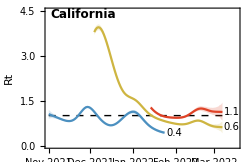
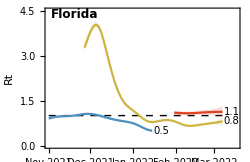
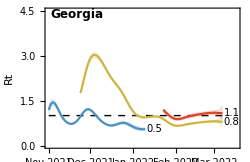
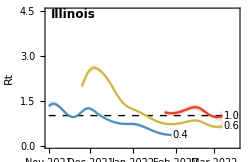
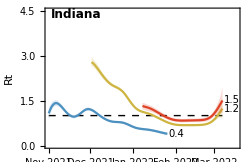
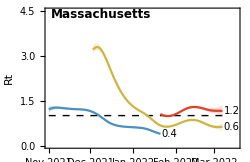
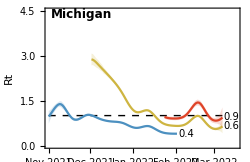
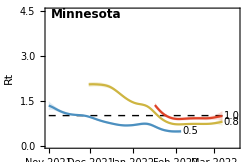
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron 21L"][[-1,1]],Round[rtGather[#,"Omicron 21L"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron 21L"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron 21L"][[-1,2]],0.1]}&,countries]
```

{California→{2022-03-07,1.1,0.8,1.4},Florida→{2022-03-07,1.1,0.9,1.3},Georgia→{2022-03-07,1.1,0.8,1.3},Illinois→{2022-03-07,1.,0.7,1.2},Indiana→{2022-03-07,1.5,1.1,2.},Massachusetts→{2022-03-07,1.2,1.,1.3},Michigan→{2022-03-07,0.9,0.6,1.3},Minnesota→{2022-03-07,1.,0.8,1.1},New Jersey→{2022-03-07,1.2,1.1,1.4},New York→{2022-03-07,1.2,1.,1.4},North Carolina→{2022-03-07,1.1,0.9,1.4},Ohio→{2022-03-07,0.8,0.6,0.9},Oregon→{2022-03-07,1.,0.9,1.2},Rhode Island→{2022-03-07,1.6,1.2,1.9},Tennessee→{2022-03-07,0.8,0.7,1.},Texas→{2022-03-07,1.2,0.9,1.5},Utah→{2022-03-07,1.2,1.1,1.3},Virginia→{2022-03-07,1.1,0.9,1.2},Washington→{2022-03-07,1.4,1.,1.8},Wisconsin→{2022-03-07,1.1,0.9,1.4}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.005];
```

```mathematica
rData=DeleteCases[rData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,16]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;4]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryLittleRPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

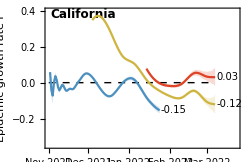
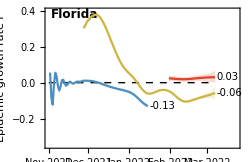
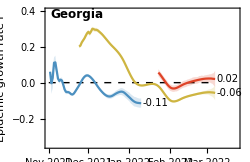
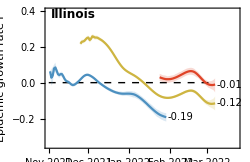
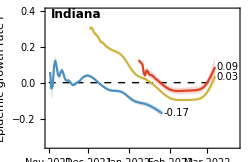
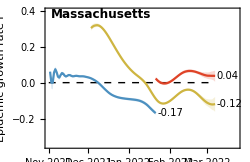
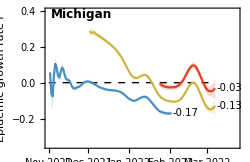
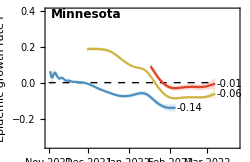
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron 21L"][[-1,1]],Round[rGather[#,"Omicron 21L"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron 21L"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron 21L"][[-1,2]],0.01]}&,countries]
```

{California→{2022-03-07,0.03,-0.02,0.08},Florida→{2022-03-07,0.03,0.,0.07},Georgia→{2022-03-07,0.02,-0.02,0.07},Illinois→{2022-03-07,-0.01,-0.05,0.02},Indiana→{2022-03-07,0.09,0.03,0.14},Massachusetts→{2022-03-07,0.04,0.,0.07},Michigan→{2022-03-07,-0.03,-0.09,0.03},Minnesota→{2022-03-07,-0.01,-0.04,0.03},New Jersey→{2022-03-07,0.05,0.03,0.08},New York→{2022-03-07,0.06,0.03,0.08},North Carolina→{2022-03-07,0.03,-0.02,0.07},Ohio→{2022-03-07,-0.06,-0.1,-0.02},Oregon→{2022-03-07,0.01,-0.01,0.05},Rhode Island→{2022-03-07,0.1,0.06,0.14},Tennessee→{2022-03-07,-0.04,-0.07,0.},Texas→{2022-03-07,0.04,-0.01,0.08},Utah→{2022-03-07,0.06,0.04,0.07},Virginia→{2022-03-07,0.02,-0.01,0.05},Washington→{2022-03-07,0.07,0.02,0.13},Wisconsin→{2022-03-07,0.03,-0.01,0.08}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron 21L"][[-1,1]],Round[Log[2]/rGather[#,"Omicron 21L"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron 21L"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron 21L"][[-1,2]],0.1]}&,countries]
```

{California→{2022-03-07,23.,8.4,-35.9},Florida→{2022-03-07,23.,10.5,-427.4},Georgia→{2022-03-07,34.,10.5,-29.4},Illinois→{2022-03-07,-66.6,29.5,-12.8},Indiana→{2022-03-07,8.,4.9,20.5},Massachusetts→{2022-03-07,18.3,10.4,150.4},Michigan→{2022-03-07,-21.6,25.,-7.6},Minnesota→{2022-03-07,-117.1,25.,-16.4},New Jersey→{2022-03-07,13.1,8.4,26.7},New York→{2022-03-07,12.2,8.3,25.5},North Carolina→{2022-03-07,24.4,9.4,-43.1},Ohio→{2022-03-07,-11.4,-29.3,-7.},Oregon→{2022-03-07,48.2,14.3,-50.5},Rhode Island→{2022-03-07,6.7,4.9,12.5},Tennessee→{2022-03-07,-17.2,-348.4,-9.5},Texas→{2022-03-07,16.2,8.4,-118.3},Utah→{2022-03-07,12.3,9.4,18.1},Virginia→{2022-03-07,34.9,13.5,-94.1},Washington→{2022-03-07,9.2,5.5,29.5},Wisconsin→{2022-03-07,23.,9.2,-74.6}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{60,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{50,1020000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

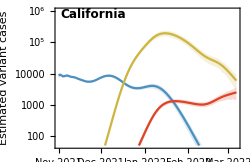
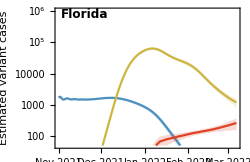
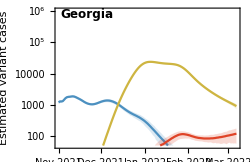
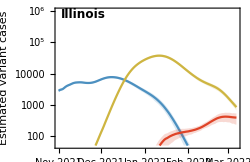
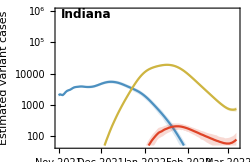
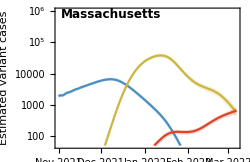
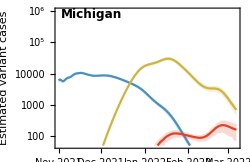
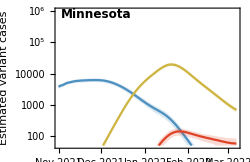
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

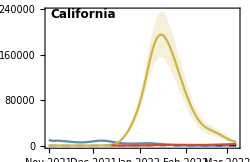
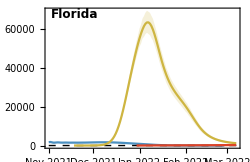
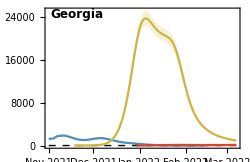
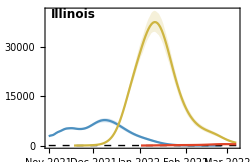
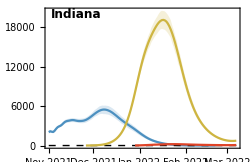
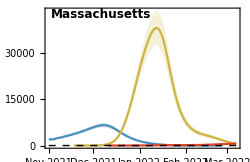
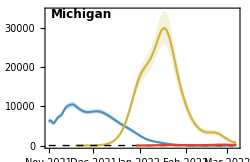
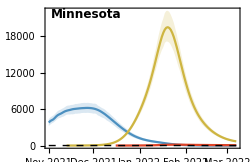
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron 21L"][[-1,1]],Round[pGather[#,"Omicron 21L"][[-1,2]]],Round[pGatherLower[#,"Omicron 21L"][[-1,2]]],Round[pGatherUpper[#,"Omicron 21L"][[-1,2]]]}&,countries]
```

{California→{2022-03-07,2518,1492,3628},Florida→{2022-03-07,263,154,368},Georgia→{2022-03-07,119,57,174},Illinois→{2022-03-07,392,233,533},Indiana→{2022-03-07,78,28,128},Massachusetts→{2022-03-07,655,487,827},Michigan→{2022-03-07,160,71,248},Minnesota→{2022-03-07,58,29,84},New Jersey→{2022-03-07,683,521,823},New York→{2022-03-07,848,624,1048},North Carolina→{2022-03-07,36,14,57},Ohio→{2022-03-07,18,7,28},Oregon→{2022-03-07,97,41,164},Rhode Island→{2022-03-07,320,240,394},Tennessee→{2022-03-07,66,26,98},Texas→{2022-03-07,463,286,664},Utah→{2022-03-07,189,105,263},Virginia→{2022-03-07,182,71,281},Washington→{2022-03-07,346,189,488},Wisconsin→{2022-03-07,81,41,118}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,2,4}]]
```

```mathematica
panels=Map[countryFrequencyPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;4]],variants[[2;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

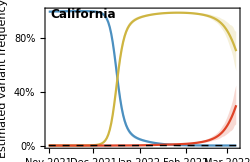
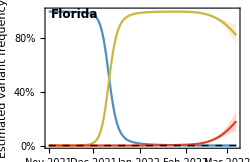
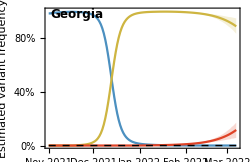
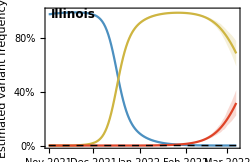
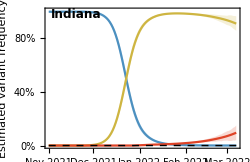
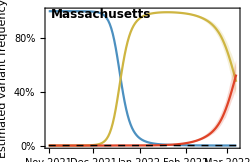
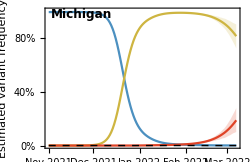
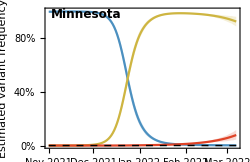
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron 21L"][[-1,1]],Round[fGather[#,"Omicron 21L"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron 21L"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron 21L"][[-1,2]],0.01]}&,countries]
```

{California→{2022-03-07,0.3,0.16,0.45},Florida→{2022-03-07,0.18,0.11,0.26},Georgia→{2022-03-07,0.12,0.06,0.17},Illinois→{2022-03-07,0.32,0.22,0.41},Indiana→{2022-03-07,0.09,0.04,0.15},Massachusetts→{2022-03-07,0.53,0.42,0.64},Michigan→{2022-03-07,0.19,0.1,0.28},Minnesota→{2022-03-07,0.08,0.04,0.11},New Jersey→{2022-03-07,0.56,0.47,0.64},New York→{2022-03-07,0.57,0.48,0.66},North Carolina→{2022-03-07,0.01,0.,0.01},Ohio→{2022-03-07,0.02,0.01,0.04},Oregon→{2022-03-07,0.16,0.06,0.25},Rhode Island→{2022-03-07,0.9,0.87,0.93},Tennessee→{2022-03-07,0.12,0.06,0.18},Texas→{2022-03-07,0.16,0.1,0.22},Utah→{2022-03-07,0.41,0.27,0.53},Virginia→{2022-03-07,0.14,0.06,0.21},Washington→{2022-03-07,0.17,0.1,0.24},Wisconsin→{2022-03-07,0.12,0.07,0.18}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[state_,variant_]:=Module[{popSize,stateName},
stateName=StringReplace[state," "->""];
popSize=QuantityMagnitude[AdministrativeDivisionData[{stateName, "UnitedStates"},"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[state,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron21K,pairsOmicron21L},
pairsOmicron21K=phaseGather[country,"Omicron 21K"];
pairsOmicron21L=phaseGather[country,"Omicron 21L"];
ListLogLinearPlot[{pairsOmicron21K,{Last[pairsOmicron21K]},pairsOmicron21L,{Last[pairsOmicron21L]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]],colors[[4]],colors[[4]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[3;;4]],variants[[3;;4]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

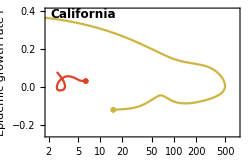
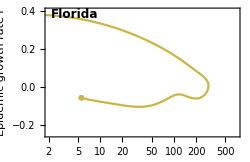
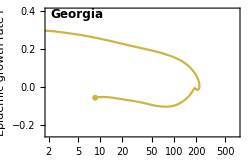
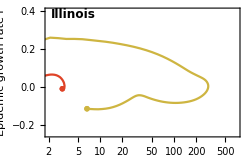
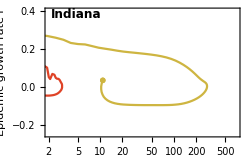
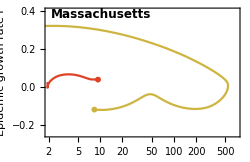
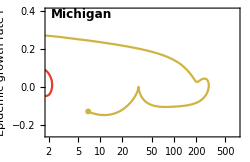
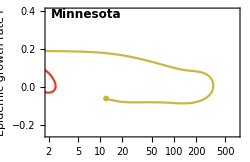
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_variant-cases-vs-rt.png